```mathematica
Needs["QuantumUtils`"]
Needs["NVHamiltonian`"]
```

```mathematica
H=NVHamiltonian[];
H //BlockForm
```

(Δ | 0 | 0
0 | 0 | 0
0 | 0 | Δ)

```mathematica
H=NVHamiltonian[MagneticField->Vector[{Bx,0,Bz},Cartesian]];
H//BlockForm
```

(Bz γe+Δ | (Bx γe)/(√2) | 0
(Bx γe)/(√2) | 0 | (Bx γe)/(√2)
0 | (Bx γe)/(√2) | -Bz γe+Δ)

```mathematica
H=NVHamiltonian[Nitrogen[15,{A,B},0],MagneticField->Vector[{Bx,0,Bz},Cartesian]];
H//BlockForm[#,2]&
```

(A/2+Bz γe+(Bz γn15)/2+Δ | (Bx γn15)/2 | (Bx γe)/(√2) | 0 | 0 | 0
(Bx γn15)/2 | -A/2+Bz γe-(Bz γn15)/2+Δ | B/(√2) | (Bx γe)/(√2) | 0 | 0
(Bx γe)/(√2) | B/(√2) | (Bz γn15)/2 | (Bx γn15)/2 | (Bx γe)/(√2) | 0
0 | (Bx γe)/(√2) | (Bx γn15)/2 | -(Bz γn15)/2 | B/(√2) | (Bx γe)/(√2)
0 | 0 | (Bx γe)/(√2) | B/(√2) | -A/2-Bz γe+(Bz γn15)/2+Δ | (Bx γn15)/2
0 | 0 | 0 | (Bx γe)/(√2) | (Bx γn15)/2 | A/2-Bz γe-(Bz γn15)/2+Δ)

```mathematica
H=NVHamiltonian[Felton09Nucleus["14N"],MagneticField->Vector[{5,0,10},Cartesian]];
H//BlockForm
```

(1.81639×10^10 | 6835.38 | 0. | 6.22558×10^7 | 0. | 0. | 0. | 0. | 0.
6835.38 | 1.82088×10^10 | 6835.38 | -1.69646×10^7 | 6.22558×10^7 | 0. | 0. | 0. | 0.
0. | 6835.38 | 1.81908×10^10 | 0. | -1.69646×10^7 | 6.22558×10^7 | 0. | 0. | 0.
6.22558×10^7 | -1.69646×10^7 | 0. | -3.14594×10^7 | 6835.38 | 0. | 6.22558×10^7 | 0. | 0.
0. | 6.22558×10^7 | -1.69646×10^7 | 6835.38 | 0. | 6835.38 | -1.69646×10^7 | 6.22558×10^7 | 0.
0. | 0. | 6.22558×10^7 | 0. | 6835.38 | -3.14981×10^7 | 0. | -1.69646×10^7 | 6.22558×10^7
0. | 0. | 0. | 6.22558×10^7 | -1.69646×10^7 | 0. | 1.78386×10^10 | 6835.38 | 0.
0. | 0. | 0. | 0. | 6.22558×10^7 | -1.69646×10^7 | 6835.38 | 1.78567×10^10 | 6835.38
0. | 0. | 0. | 0. | 0. | 6.22558×10^7 | 0. | 6835.38 | 1.78117×10^10)

```mathematica
Tensor[DipoleCarbon[Vector[{5,0,10},Cartesian]]]//MatrixForm
```

((γc γe μ0 ℏ)/(3125 √5 λ^3) | 0 | -(3 γc γe μ0 ℏ)/(3125 √5 λ^3)
0 | (γc γe μ0 ℏ)/(1250 √5 λ^3) | 0
-(3 γc γe μ0 ℏ)/(3125 √5 λ^3) | 0 | -(7 γc γe μ0 ℏ)/(6250 √5 λ^3))

```mathematica
order=1;
ωuw=Δ-γe Bz;
H=NVAverageHamiltonian[order,ωuw,MagneticField->Vector[{2Ω Cos[ωuw t]/γe,0,Bz},Cartesian]];
H//FullSimplify//BlockForm
```

(2 Bz γe-(Δ Ω^2)/(4 (-Bz γe+Δ)^2) | -(Ω (2 Bz^2 γe^2+4 Bz γe Δ-4 Δ^2+Ω^2))/(4 √2 (-Bz γe+Δ)^2) | ((Bz γe-2 Δ) Ω^2)/(8 (-Bz γe+Δ)^2)
-(Ω (2 Bz^2 γe^2+4 Bz γe Δ-4 Δ^2+Ω^2))/(4 √2 (-Bz γe+Δ)^2) | -((Bz γe-2 Δ) Ω^2)/(4 (-Bz γe+Δ)^2) | (Ω (4-Ω^2/(-Bz γe+Δ)^2))/(4 √2)
((Bz γe-2 Δ) Ω^2)/(8 (-Bz γe+Δ)^2) | (Ω (4-Ω^2/(-Bz γe+Δ)^2))/(4 √2) | Ω^2/(4 Bz γe-4 Δ))

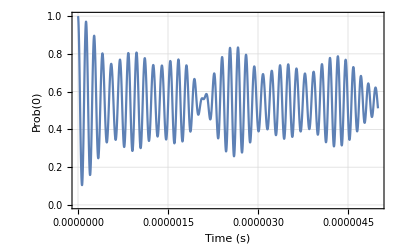

```mathematica
staticField={1,20,50};
ωuw=Δ-γe Last[staticField];
H=NVAverageHamiltonian[
2,ωuw,
Taminiau12Nucleus[3],
DipoleCarbon[Vector[{1,0,2},Cartesian]],
Felton09Nucleus["14N"],
MagneticField->Vector[{10 10^6 Cos[2π ωuw t]/γe,0,0}+staticField,Cartesian]
];
data=PulseSim[H,5 10^-6,
InitialState->Projector[{0,1,0}]⊗Subscript[𝟙, 12]/12,
Observables->{Projector[{0,1,0}]⊗Subscript[𝟙, 12]},
PollingInterval->2 10^-9
];
ListPlot[
Observables[data,TimeVector->True],
Joined->True,
FrameLabel->{"Time (s)","Prob(0)"},PlotTheme->"Detailed"
]
```